## Dipole v2, |J|^2 at large kT

```mathematica
Quit[]
```

### |J|^2 at large kT

```mathematica
ClearAll[SP];
SP[x_]:=SP[x,x];
SP[x_,y1_+y2_]:=SP[x,y1]+SP[x,y2];
SP[x1_+x2_,y_]:=SP[x1,y]+SP[x2,y];
SP[x_,-y_]:=-SP[x,y];
SP[-x_,y_]:=-SP[x,y];
SP[x_,k]/;!FreeQ[{x1,x2,x3,x4},x]:=SP[k,x];
SP[x_,x1]/;!FreeQ[{x2,x3,x4},x]:=SP[x1,x];
SP[x_,x2]/;!FreeQ[{x3,x4},x]:=SP[x2,x];
SP[x4,x3]:=SP[x3,x4];
SP[ϵ x_,y_]:=ϵ SP[x,y];
SP[x_,ϵ y_]:=ϵ SP[x,y];
```

```mathematica
ClearAll[MyresT1];
MyresT1=2/(2π)^2 1/SP[k]^2((1+cb31)/b31^2+(1+cb41)/b41^2+(1+cb32)/b32^2+(1+cb42)/b42^2+(x34^2-b31^2-b41^2)/(2 b31^2 b41^2)(1+cb31+cb41+c34)+(x12^2-b31^2-b32^2)/(2 b31^2 b32^2)(1+cb31+cb32+c12)-(x1432^2-b31^2-b42^2)/(2 b31^2 b42^2)(c12+cb32+cb41+c34)-(x1342^2-b41^2-b32^2)/(2 b32^2 b41^2)(c12+cb42+cb31+c34)+(x12^2-b41^2-b42^2)/(2 b41^2 b42^2)(1+cb41+cb42+c12)+(x34^2-b32^2-b42^2)/(2 b32^2 b42^2)(1+cb32+cb42+c34));
```

```mathematica
ClearAll[MyresT2];
MyresT2=-1/π^2 1/SP[k]^3((SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c31-(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c32-(SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c41+(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c42);
```

```mathematica
ClearAll[Myres];
Myres=MyresT1+MyresT2/.{cb31:>c31,cb41:>c41,cb32:>c32,cb42:>c42,b31:>√SP[x31],b32:>√SP[x32],b41:>√SP[x41],b42:>√SP[x42],x1432:>√SP[x1432],x1342:>√SP[x1342],x12:>√SP[x12],x34:>√SP[x34]}/.{x1342:>x32-x41,x1432:>x42-x31}/.{c31:>Cos[SP[k,x31]],c32:>Cos[SP[k,x32]],c12:>Cos[SP[k,x12]],c41:>Cos[SP[k,x41]],c42:>Cos[SP[k,x42]],c34:>Cos[SP[k,x34]]};
```

```mathematica
Myres
```

1/(2 π^2 (SP(k,k))^2)(-((-SP(x32,x41)-SP(x41,x32)) (cos(SP(k,x12))+cos(SP(k,x31))+cos(SP(k,x34))+cos(SP(k,x42))))/(2 SP(x32,x32) SP(x41,x41))-((-SP(x31,x42)-SP(x42,x31)) (cos(SP(k,x12))+cos(SP(k,x32))+cos(SP(k,x34))+cos(SP(k,x41))))/(2 SP(x31,x31) SP(x42,x42))+((SP(x12,x12)-SP(x31,x31)-SP(x32,x32)) (cos(SP(k,x12))+cos(SP(k,x31))+cos(SP(k,x32))+1))/(2 SP(x31,x31) SP(x32,x32))+((SP(x12,x12)-SP(x41,x41)-SP(x42,x42)) (cos(SP(k,x12))+cos(SP(k,x41))+cos(SP(k,x42))+1))/(2 SP(x41,x41) SP(x42,x42))+((-SP(x31,x31)+SP(x34,x34)-SP(x41,x41)) (cos(SP(k,x31))+cos(SP(k,x34))+cos(SP(k,x41))+1))/(2 SP(x31,x31) SP(x41,x41))+(cos(SP(k,x31))+1)/(SP(x31,x31))+((-SP(x32,x32)+SP(x34,x34)-SP(x42,x42)) (cos(SP(k,x32))+cos(SP(k,x34))+cos(SP(k,x42))+1))/(2 SP(x32,x32) SP(x42,x42))+(cos(SP(k,x32))+1)/(SP(x32,x32))+(cos(SP(k,x41))+1)/(SP(x41,x41))+(cos(SP(k,x42))+1)/(SP(x42,x42)))-1/(π^2 (SP(k,k))^3)(((SP(k,x31))/(SP(x31,x31))-(SP(k,x32))/(SP(x32,x32))) ((SP(k,x31))/(SP(x31,x31))-(SP(k,x41))/(SP(x41,x41))) cos(SP(k,x31))-((SP(k,x31))/(SP(x31,x31))-(SP(k,x32))/(SP(x32,x32))) ((SP(k,x32))/(SP(x32,x32))-(SP(k,x42))/(SP(x42,x42))) cos(SP(k,x32))-((SP(k,x31))/(SP(x31,x31))-(SP(k,x41))/(SP(x41,x41))) ((SP(k,x41))/(SP(x41,x41))-(SP(k,x42))/(SP(x42,x42))) cos(SP(k,x41))+((SP(k,x32))/(SP(x32,x32))-(SP(k,x42))/(SP(x42,x42))) ((SP(k,x41))/(SP(x41,x41))-(SP(k,x42))/(SP(x42,x42))) cos(SP(k,x42)))

```mathematica
Variables[Myres/.SP[x_,y_]:>x y/.Cos[x_]:>x]
```

{k,x31,x32,x41,x42,x12,x34}

```mathematica
ClearAll[INT];
INT[x_*y_]/;FreeQ[x,SP[k,x31]|SP[k,x32]|SP[k,x41]|SP[k,x42]|SP[k,x12]|SP[k,x34]]:=x*INT[y];
INT[x_+y_]:=INT[x]+INT[y];
INT[x_]/;x=!=1&&FreeQ[x,SP[k,x31]|SP[k,x32]|SP[k,x41]|SP[k,x42]|SP[k,x12]|SP[k,x34]]:=x*INT[1]
```

```mathematica
ClearAll[Myres1];
Myres1=INT[Myres//Expand]
```

-(INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x31,x31))+(SP(x12,x12) INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x32,x32))-(INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x32,x32))+(SP(x32,x41) INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x41,x41))+(SP(x41,x32) INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x41,x41))-(INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x41,x41))+(SP(x31,x42) INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x42,x42))+(SP(x42,x31) INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x42,x42))+(SP(x12,x12) INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x41,x41) SP(x42,x42))-(INT(cos(SP(k,x12))))/(4 π^2 (SP(k,k))^2 SP(x42,x42))-(INT(cos(SP(k,x32))))/(4 π^2 (SP(k,k))^2 SP(x31,x31))-(INT(cos(SP(k,x34))))/(4 π^2 (SP(k,k))^2 SP(x31,x31))-(INT(cos(SP(k,x41))))/(4 π^2 (SP(k,k))^2 SP(x31,x31))+(INT(1) SP(x12,x12))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x32,x32))+(INT(cos(SP(k,x31))) SP(x12,x12))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x32,x32))+(INT(cos(SP(k,x32))) SP(x12,x12))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x32,x32))+(INT(cos(SP(k,x31)) SP(k,x31) SP(k,x32)))/(π^2 (SP(k,k))^3 SP(x31,x31) SP(x32,x32))+(INT(cos(SP(k,x32)) SP(k,x31) SP(k,x32)))/(π^2 (SP(k,k))^3 SP(x31,x31) SP(x32,x32))-(INT(cos(SP(k,x31))))/(4 π^2 (SP(k,k))^2 SP(x32,x32))-(INT(cos(SP(k,x34))))/(4 π^2 (SP(k,k))^2 SP(x32,x32))-(INT(cos(SP(k,x42))))/(4 π^2 (SP(k,k))^2 SP(x32,x32))+(INT(cos(SP(k,x31))) SP(x32,x41))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x41,x41))+(INT(cos(SP(k,x34))) SP(x32,x41))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x41,x41))+(INT(cos(SP(k,x42))) SP(x32,x41))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x41,x41))+(INT(1) SP(x34,x34))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x41,x41))+(INT(cos(SP(k,x31))) SP(x34,x34))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x41,x41))+(INT(cos(SP(k,x34))) SP(x34,x34))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x41,x41))+(INT(cos(SP(k,x41))) SP(x34,x34))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x41,x41))+(INT(cos(SP(k,x31))) SP(x41,x32))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x41,x41))+(INT(cos(SP(k,x34))) SP(x41,x32))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x41,x41))+(INT(cos(SP(k,x42))) SP(x41,x32))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x41,x41))+(INT(cos(SP(k,x31)) SP(k,x31) SP(k,x41)))/(π^2 (SP(k,k))^3 SP(x31,x31) SP(x41,x41))+(INT(cos(SP(k,x41)) SP(k,x31) SP(k,x41)))/(π^2 (SP(k,k))^3 SP(x31,x31) SP(x41,x41))-(INT(cos(SP(k,x31)) SP(k,x32) SP(k,x41)))/(π^2 (SP(k,k))^3 SP(x32,x32) SP(x41,x41))-(INT(cos(SP(k,x42)) SP(k,x32) SP(k,x41)))/(π^2 (SP(k,k))^3 SP(x32,x32) SP(x41,x41))-(INT(cos(SP(k,x31))))/(4 π^2 (SP(k,k))^2 SP(x41,x41))-(INT(cos(SP(k,x34))))/(4 π^2 (SP(k,k))^2 SP(x41,x41))-(INT(cos(SP(k,x42))))/(4 π^2 (SP(k,k))^2 SP(x41,x41))+(INT(cos(SP(k,x32))) SP(x31,x42))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x42,x42))+(INT(cos(SP(k,x34))) SP(x31,x42))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x42,x42))+(INT(cos(SP(k,x41))) SP(x31,x42))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x42,x42))+(INT(1) SP(x34,x34))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x42,x42))+(INT(cos(SP(k,x32))) SP(x34,x34))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x42,x42))+(INT(cos(SP(k,x34))) SP(x34,x34))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x42,x42))+(INT(cos(SP(k,x42))) SP(x34,x34))/(4 π^2 (SP(k,k))^2 SP(x32,x32) SP(x42,x42))+(INT(cos(SP(k,x32))) SP(x42,x31))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x42,x42))+(INT(cos(SP(k,x34))) SP(x42,x31))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x42,x42))+(INT(cos(SP(k,x41))) SP(x42,x31))/(4 π^2 (SP(k,k))^2 SP(x31,x31) SP(x42,x42))-(INT(cos(SP(k,x32)) SP(k,x31) SP(k,x42)))/(π^2 (SP(k,k))^3 SP(x31,x31) SP(x42,x42))-(INT(cos(SP(k,x41)) SP(k,x31) SP(k,x42)))/(π^2 (SP(k,k))^3 SP(x31,x31) SP(x42,x42))+(INT(cos(SP(k,x32)) SP(k,x32) SP(k,x42)))/(π^2 (SP(k,k))^3 SP(x32,x32) SP(x42,x42))+(INT(cos(SP(k,x42)) SP(k,x32) SP(k,x42)))/(π^2 (SP(k,k))^3 SP(x32,x32) SP(x42,x42))+(INT(1) SP(x12,x12))/(4 π^2 (SP(k,k))^2 SP(x41,x41) SP(x42,x42))+(INT(cos(SP(k,x41))) SP(x12,x12))/(4 π^2 (SP(k,k))^2 SP(x41,x41) SP(x42,x42))+(INT(cos(SP(k,x42))) SP(x12,x12))/(4 π^2 (SP(k,k))^2 SP(x41,x41) SP(x42,x42))+(INT(cos(SP(k,x41)) SP(k,x41) SP(k,x42)))/(π^2 (SP(k,k))^3 SP(x41,x41) SP(x42,x42))+(INT(cos(SP(k,x42)) SP(k,x41) SP(k,x42)))/(π^2 (SP(k,k))^3 SP(x41,x41) SP(x42,x42))-(INT(cos(SP(k,x32))))/(4 π^2 (SP(k,k))^2 SP(x42,x42))-(INT(cos(SP(k,x34))))/(4 π^2 (SP(k,k))^2 SP(x42,x42))-(INT(cos(SP(k,x41))))/(4 π^2 (SP(k,k))^2 SP(x42,x42))-(INT(cos(SP(k,x31)) (SP(k,x31))^2))/(π^2 (SP(k,k))^3 (SP(x31,x31))^2)-(INT(cos(SP(k,x32)) (SP(k,x32))^2))/(π^2 (SP(k,k))^3 (SP(x32,x32))^2)-(INT(cos(SP(k,x41)) (SP(k,x41))^2))/(π^2 (SP(k,k))^3 (SP(x41,x41))^2)-(INT(cos(SP(k,x42)) (SP(k,x42))^2))/(π^2 (SP(k,k))^3 (SP(x42,x42))^2)

```mathematica
Myres1//Variables//Select[#,#1[[0]]===INT&]&//Sort
```

{INT(1),INT(cos(SP(k,x12))),INT(cos(SP(k,x31))),INT(cos(SP(k,x32))),INT(cos(SP(k,x34))),INT(cos(SP(k,x41))),INT(cos(SP(k,x42))),INT((SP(k,x31))^2 cos(SP(k,x31))),INT(SP(k,x31) SP(k,x32) cos(SP(k,x31))),INT(SP(k,x31) SP(k,x32) cos(SP(k,x32))),INT((SP(k,x32))^2 cos(SP(k,x32))),INT(SP(k,x31) SP(k,x41) cos(SP(k,x31))),INT(SP(k,x31) SP(k,x41) cos(SP(k,x41))),INT(SP(k,x32) SP(k,x41) cos(SP(k,x31))),INT(SP(k,x32) SP(k,x41) cos(SP(k,x42))),INT((SP(k,x41))^2 cos(SP(k,x41))),INT(SP(k,x31) SP(k,x42) cos(SP(k,x32))),INT(SP(k,x31) SP(k,x42) cos(SP(k,x41))),INT(SP(k,x32) SP(k,x42) cos(SP(k,x32))),INT(SP(k,x32) SP(k,x42) cos(SP(k,x42))),INT(SP(k,x41) SP(k,x42) cos(SP(k,x41))),INT(SP(k,x41) SP(k,x42) cos(SP(k,x42))),INT((SP(k,x42))^2 cos(SP(k,x42)))}

```mathematica
Myres1//Variables//Select[#,#1[[0]]=!=INT&]&//Sort
```

{SP(k,k),SP(x12,x12),SP(x31,x31),SP(x31,x42),SP(x32,x32),SP(x32,x41),SP(x34,x34),SP(x41,x32),SP(x41,x41),SP(x42,x31),SP(x42,x42)}

```mathematica
ClearAll[Toθ];
Toθ[x_]:=StringJoin["θ",ToString[x]//StringDrop[#,1]&]//ToExpression;
```

```mathematica
ClearAll[rplcSigma];
rplcSigma={INT2[1]:>2π,INT2[Cos[SP[k,x_]]]:>2π BesselJ[0,A[k]A[x]],INT2[Cos[SP[k,x1_]]SP[k,x2_]SP[k,x3_]]:>A[k]^2 A[x2]A[x3]((2π)/(A[k]A[x1])BesselJ[1,A[k]A[x1]]Cos[Toθ[x2]-Toθ[x3]]-2π BesselJ[2,A[k]A[x1]]Cos[Toθ[x2]-Toθ[x1]]Cos[Toθ[x3]-Toθ[x1]]),
INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[k]^2 A[x2]^2((2π)/(A[k]A[x1])BesselJ[1,A[k]A[x1]]-2π BesselJ[2,A[k]A[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)}
```

{INT2(1):>2 π,INT2(cos(SP(k,x_))):>2 π 0A(k) A(x),INT2(SP(k,x2_) SP(k,x3_) cos(SP(k,x1_))):>(A(k))^2 A(x2) A(x3) (((2 π) 1A(k) A(x1) cos(Toθ(x2)-Toθ(x3)))/(A(k) A(x1))-2 π 2A(k) A(x1) cos(Toθ(x2)-Toθ(x1)) cos(Toθ(x3)-Toθ(x1))),INT2((SP(k,x2_))^2 cos(SP(k,x1_))):>(A(k))^2 (A(x2))^2 (((2 π) 1A(k) A(x1))/(A(k) A(x1))-2 π 2A(k) A(x1) cos^2(Toθ(x2)-Toθ(x1)))}

```mathematica
ClearAll[rplc0];
rplc0={SP[x42,x31]:>SP[x31,x42],SP[x41,x32]:>SP[x32,x41],SP[x_,x_]:>A[x]^2};
```

```mathematica
ClearAll[σAvg];
σAvg=Myres1/.INT:>INT2/.rplcSigma/.rplc0//Together;
```

```mathematica
ClearAll[rplcV2];
rplcV2={INT2[1]:>0,INT2[Cos[SP[k,x_]]]:>-2π BesselJ[2,A[k]A[x]]Cos[2Toθ[x]],INT2[Cos[SP[k,x1_]]SP[k,x2_]SP[k,x3_]]:>A[x2]A[x3] π/A[x1]^2(2BesselJ[2,A[k]A[x1]](6Cos[Toθ[x2]+Toθ[x3]-4Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2Toθ[x1]]Cos[Toθ[x2]-Toθ[x1]]Cos[Toθ[x3]-Toθ[x1]])+A[k]A[x1]BesselJ[1,A[k]A[x1]](Cos[Toθ[x2]+Toθ[x3]]-3Cos[Toθ[x2]+Toθ[x3]-4Toθ[x1]])),
INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[x2]^2 π/A[x1]^2(2BesselJ[2,A[k]A[x1]](6Cos[2Toθ[x2]-4Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)+A[k]A[x1]BesselJ[1,A[k]A[x1]](Cos[2Toθ[x2]]-3Cos[2Toθ[x2]-4Toθ[x1]]))}
```

{INT2(1):>0,INT2(cos(SP(k,x_))):>-2 π cos(2 Toθ(x)) 2A(k) A(x),INT2(SP(k,x2_) SP(k,x3_) cos(SP(k,x1_))):>1/(A(x1))^2 π A(x2) A(x3) (2 2A(k) A(x1) (6 cos(-4 Toθ(x1)+Toθ(x2)+Toθ(x3))-(A(k))^2 (A(x1))^2 cos(2 Toθ(x1)) cos(Toθ(x2)-Toθ(x1)) cos(Toθ(x3)-Toθ(x1)))+A(k) A(x1) 1A(k) A(x1) (cos(Toθ(x2)+Toθ(x3))-3 cos(-4 Toθ(x1)+Toθ(x2)+Toθ(x3)))),INT2((SP(k,x2_))^2 cos(SP(k,x1_))):>(π (A(x2))^2 (2 2A(k) A(x1) (6 cos(2 Toθ(x2)-4 Toθ(x1))-(A(k))^2 (A(x1))^2 cos(2 Toθ(x1)) cos^2(Toθ(x2)-Toθ(x1)))+A(k) A(x1) 1A(k) A(x1) (cos(2 Toθ(x2))-3 cos(2 Toθ(x2)-4 Toθ(x1)))))/(A(x1))^2}

```mathematica
ClearAll[Avg2θk];
Avg2θk=Myres1/.INT:>INT2/.rplcV2/.rplc0//Together;
```

```mathematica
ClearAll[VarσAvg];
VarσAvg=Variables[σAvg]/.BesselJ[_,x_]:>x/.Cos[x_]:>x//Variables//DeleteDuplicates//Sort
```

{θ31,θ32,θ41,θ42,A(k),A(x12),A(x31),A(x32),A(x34),A(x41),A(x42),SP(x31,x42),SP(x32,x41)}

```mathematica
ClearAll[VarAvg2θk];
VarAvg2θk=Variables[Avg2θk]/.BesselJ[_,x_]:>x/.Cos[x_]:>x//Variables//DeleteDuplicates//Sort
```

{θ12,θ31,θ32,θ34,θ41,θ42,A(k),A(x12),A(x31),A(x32),A(x34),A(x41),A(x42),SP(x31,x42),SP(x32,x41)}

```mathematica
SubsetQ[VarAvg2θk,VarσAvg]
```

True

### Create Code Input

```mathematica
σAvg//InputForm
```

(A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42] + A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3 + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3 + 
  A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x12]] + 
  A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]] + 
  A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x31]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x31]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]] + 
  A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x32]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x32]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x34]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x41]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x41]] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x41]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x41]] + 
  A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x42]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x42]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x42]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x42]] - 
  4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x31]] - 4*A[x31]^3*A[x41]^3*A[x42]^3*
   BesselJ[1, A[k]*A[x32]] - 4*A[x31]^3*A[x32]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]] - 
  4*A[x31]^3*A[x32]^3*A[x41]^3*BesselJ[1, A[k]*A[x42]] + 4*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*
   BesselJ[2, A[k]*A[x31]] + 4*A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x32]] + 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[2, A[k]*A[x41]] + 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[2, A[k]*A[x42]] + 
  4*A[x31]*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ31 - θ32] + 
  4*A[x31]^2*A[x32]*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - θ32] - 
  4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ32] - 
  4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32] + 
  4*A[x31]*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ31 - θ41] + 
  4*A[x31]^2*A[x32]^3*A[x41]*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - θ41] - 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ41] - 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41] + 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ32]*Cos[θ31 - θ41] - 
  4*A[x31]^2*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ32 - θ41] - 
  4*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - θ41] - 
  4*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - θ42] - 
  4*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - θ42] + 
  4*A[x31]^3*A[x32]*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x32]]*Cos[θ32 - θ42] + 
  4*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - θ42] - 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[θ32 - θ42] - 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42] + 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[θ32 - θ42] + 
  4*A[x31]^3*A[x32]^3*A[x41]*A[x42]^2*BesselJ[1, A[k]*A[x41]]*Cos[θ41 - θ42] + 
  4*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[θ41 - θ42] - 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[θ41 - θ42] - 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - θ42] + 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[θ41 - θ42] + 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[θ41 - θ42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x12]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x41]]*SP[x31, x42] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x12]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x42]]*SP[x32, x41])/
 (2*Pi*A[k]^5*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^3)

```mathematica
Avg2θk//InputForm
```

(-(A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]) + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] - 
  A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  4*A[k]*A[x31]*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[2*θ31] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  24*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] + 
  4*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  6*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - 3*θ32] + 
  24*A[x31]^3*A[x32]*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - 3*θ32] - 
  4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ32] - 
  6*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[3*θ31 - θ32] + 
  24*A[x31]*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[3*θ31 - θ32] + 
  4*A[k]*A[x31]^4*A[x32]*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[2*θ32] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  24*A[x31]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] + 
  4*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[2*θ32] + 
  2*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ31 + θ32] + 
  2*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[θ31 + θ32] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  6*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - 3*θ41] + 
  24*A[x31]^3*A[x32]^4*A[x41]*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - 3*θ41] - 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ41] + 
  4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ32]*
   Cos[θ31 - θ41] - 6*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*
   Cos[3*θ31 - θ41] + 24*A[x31]*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[3*θ31 - θ41] + 
  6*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[4*θ31 - θ32 - θ41] - 
  24*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[4*θ31 - θ32 - θ41] + 
  4*A[k]*A[x31]^4*A[x32]^4*A[x41]*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[2*θ41] - 
  A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  24*A[x31]^4*A[x32]^4*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[2*θ41] + 
  2*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ31 + θ41] + 
  2*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[θ31 + θ41] - 
  2*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ32 + θ41] - 
  2*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ41] + 
  6*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ41 - 4*θ42] - 
  24*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ32 + θ41 - 4*θ42] - 
  6*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - 3*θ42] + 
  24*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - 3*θ42] - 
  6*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ41 - 3*θ42] + 
  24*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - 3*θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32]*Cos[θ32 - θ42] + 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[2*θ32]*
   Cos[θ32 - θ42] - 6*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*
   Cos[3*θ32 - θ42] + 24*A[x31]^4*A[x32]*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[3*θ32 - θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41]*Cos[θ41 - θ42] + 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[2*θ41]*
   Cos[θ41 - θ42] - 6*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x41]]*
   Cos[3*θ41 - θ42] + 24*A[x31]^4*A[x32]^4*A[x41]*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[3*θ41 - θ42] + 
  4*A[k]*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[2*θ42] - 
  24*A[x31]^4*A[x32]^4*A[x41]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 
  A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[2*θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - θ42]*Cos[2*θ42] + 
  4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[θ41 - θ42]*
   Cos[2*θ42] - 2*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 + θ42] - 
  2*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 + θ42] + 
  6*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - 4*θ32 + θ42] - 
  24*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - 4*θ32 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ32 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ42] + 
  6*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - 4*θ41 + θ42] - 
  24*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - 4*θ41 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ41 + θ42] + 
  2*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ41 + θ42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42]*SP[x32, x41])/
 (2*Pi*A[k]^6*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^4)

### Integration for σ

```mathematica
Integrate[Cos[kx Cos[θk-θ1]],{θk,0,2π},Assumptions->kx>0]
```

2 π 0kx

```mathematica
Integrate[Cos[kx Cos[θk]]Cos[θk-θ2]Cos[θk-θ3],{θk,0,2π},Assumptions->kx>0]
```

(2 π 1kx cos(θ2-θ3))/kx-2 π cos(θ2) cos(θ3) 2kx

```mathematica
INT2[1]/.rplcSigma
```

2 π

```mathematica
INT2[Cos[SP[k,x31]]]/.rplcSigma
```

2 π 0A(k) A(x31)

```mathematica
INT2[Cos[SP[k,x32]]]/.rplcSigma
```

2 π 0A(k) A(x32)

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]SP[k,x3]]/.rplcSigma
```

(A(k))^2 A(x2) A(x3) ((2 π cos(θ2-θ3) 1A(k) A(x1))/(A(k) A(x1))-2 π cos(θ1-θ2) cos(θ1-θ3) 2A(k) A(x1))

```mathematica
INT2[Cos[SP[k,x3]]SP[k,x2]SP[k,x4]]/.rplcSigma
```

(A(k))^2 A(x2) A(x4) ((2 π cos(θ2-θ4) 1A(k) A(x3))/(A(k) A(x3))-2 π cos(θ2-θ3) cos(θ3-θ4) 2A(k) A(x3))

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]^2]/.rplcSigma
```

(A(k))^2 (A(x2))^2 ((2 π 1A(k) A(x1))/(A(k) A(x1))-2 π cos^2(θ1-θ2) 2A(k) A(x1))

```mathematica
INT2[Cos[SP[k,x3]]SP[k,x2]^2]/.rplcSigma
```

(A(k))^2 (A(x2))^2 ((2 π 1A(k) A(x3))/(A(k) A(x3))-2 π cos^2(θ2-θ3) 2A(k) A(x3))

### Integration for v2

```mathematica
Integrate[Cos[2θk],{θk,0,2π}]
```

0

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

-2 π cos(2 θx) 2Abs[kx]

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[θk-θ1]Cos[θk-θ2]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

(π (2 2kx (6 cos(θ1+θ2-4 θx)-kx^2 cos(2 θx) cos(θ1-θx) cos(θ2-θx))+kx 1kx (cos(θ1+θ2)-3 cos(θ1+θ2-4 θx))))/kx^2

```mathematica
INT2[Cos[SP[k,x31]]]/.rplcV2
```

-2 π cos(2 θ31) 2A(k) A(x31)

```mathematica
INT2[Cos[SP[k,x32]]]/.rplcV2
```

-2 π cos(2 θ32) 2A(k) A(x32)

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]SP[k,x3]]/.rplcV2;
%/(A[k]^2 A[x2]A[x3])/.{A[x1]:>kx/A[k](*,θ1:>θx,θ2:>θ1,θ3:>θ2*)}
```

(π (2 2kx (6 cos(4 θ1-θ2-θ3)-kx^2 cos(2 θ1) cos(θ1-θ2) cos(θ1-θ3))+kx 1kx (cos(θ2+θ3)-3 cos(4 θ1-θ2-θ3))))/kx^2

```mathematica
INT2[Cos[SP[k,x2]]SP[k,x3]SP[k,x4]]/.rplcV2;
%/(A[k]^2 A[x4]A[x3])/.{A[x2]:>kx/A[k](*,θ1:>θx,θ2:>θ1,θ3:>θ2*)}
```

(π (2 2kx (6 cos(4 θ2-θ3-θ4)-kx^2 cos(2 θ2) cos(θ2-θ3) cos(θ2-θ4))+kx 1kx (cos(θ3+θ4)-3 cos(4 θ2-θ3-θ4))))/kx^2

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]^2]/.rplcV2;
%/(A[k]^2 A[x2]A[x3])/.{A[x1]:>kx/A[k],θ1:>θx,θ2:>θ1,θ3:>θ2}
```

(π (2 2kx (6 cos(2 θ1-4 θx)-kx^2 cos(2 θx) cos^2(θ1-θx))+kx 1kx (cos(2 θ1)-3 cos(2 θ1-4 θx))))/kx^2

### Code: DipoleV2LargeN

```mathematica
ToPolarCoordinates[{1,2}]
```

{√5,tan^-1(2)}

```mathematica
ClearAll[DipoleV2Large];
DipoleV2Large=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{A,x12,x31,x32,x34,x41,x42,θ12,θ31,θ32,θ34,θ41,θ42,k,avg,avg2θk,SP},

{A[x12],θ12}=ToPolarCoordinates[{x1x-x2x,x1y-x2y}];
{A[x31],θ31}=ToPolarCoordinates[{x3x-x1x,x3y-x1y}];
{A[x32],θ32}=ToPolarCoordinates[{x3x-x2x,x3y-x2y}];
{A[x34],θ34}=ToPolarCoordinates[{x3x-x4x,x3y-x4y}];
{A[x41],θ41}=ToPolarCoordinates[{x4x-x1x,x4y-x1y}];
{A[x42],θ42}=ToPolarCoordinates[{x4x-x2x,x4y-x2y}];
A[k]=k0;
SP[x31,x42]={x3x-x1x,x3y-x1y}.{x4x-x2x,x4y-x2y};
SP[x32,x41]={x3x-x2x,x3y-x2y}.{x4x-x1x,x4y-x1y};

avg=(A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x12]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x31]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x31]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x32]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x32]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x34]]+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x41]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x41]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x41]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x41]]+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x42]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x42]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x42]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x42]]-4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x31]]-4*A[x31]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x32]]-4*A[x31]^3*A[x32]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]-4*A[x31]^3*A[x32]^3*A[x41]^3*BesselJ[1,A[k]*A[x42]]+4*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x31]]+4*A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x32]]+4*A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[2,A[k]*A[x41]]+4*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[2,A[k]*A[x42]]+4*A[x31]*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ31-θ32]+4*A[x31]^2*A[x32]*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31-θ32]-4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ32]-4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]+4*A[x31]*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ31-θ41]+4*A[x31]^2*A[x32]^3*A[x41]*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31-θ41]-4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ41]-4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]+4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ32]*Cos[θ31-θ41]-4*A[x31]^2*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ32-θ41]-4*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32-θ41]-4*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x32]]*Cos[θ31-θ42]-4*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[1,A[k]*A[x41]]*Cos[θ31-θ42]+4*A[x31]^3*A[x32]*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x32]]*Cos[θ32-θ42]+4*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[θ32-θ42]-4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[θ32-θ42]-4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]+4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[θ32-θ42]+4*A[x31]^3*A[x32]^3*A[x41]*A[x42]^2*BesselJ[1,A[k]*A[x41]]*Cos[θ41-θ42]+4*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[θ41-θ42]-4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[θ41-θ42]-4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ41-θ42]+4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[θ41-θ42]+4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[θ41-θ42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x12]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x41]]*SP[x31,x42]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x12]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x42]]*SP[x32,x41])/(2*Pi*A[k]^5*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^3);

avg2θk=(-(A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12])+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+4*A[k]*A[x31]*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[2*θ31]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-24*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]+4*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-6*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[θ31-3*θ32]+24*A[x31]^3*A[x32]*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[θ31-3*θ32]-4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ32]-6*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[3*θ31-θ32]+24*A[x31]*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[3*θ31-θ32]+4*A[k]*A[x31]^4*A[x32]*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[2*θ32]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-24*A[x31]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]+4*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[2*θ32]+2*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ31+θ32]+2*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[θ31+θ32]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-6*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[θ31-3*θ41]+24*A[x31]^3*A[x32]^4*A[x41]*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[θ31-3*θ41]-4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ41]+4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ32]*Cos[θ31-θ41]-6*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[3*θ31-θ41]+24*A[x31]*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[3*θ31-θ41]+6*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[4*θ31-θ32-θ41]-24*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[4*θ31-θ32-θ41]+4*A[k]*A[x31]^4*A[x32]^4*A[x41]*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[2*θ41]-A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-24*A[x31]^4*A[x32]^4*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[2*θ41]+2*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ31+θ41]+2*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[θ31+θ41]-2*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ32+θ41]-2*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ41]+6*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ41-4*θ42]-24*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ32+θ41-4*θ42]-6*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32-3*θ42]+24*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]*BesselJ[2,A[k]*A[x42]]*Cos[θ32-3*θ42]-6*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ41-3*θ42]+24*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]*BesselJ[2,A[k]*A[x42]]*Cos[θ41-3*θ42]-4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]*Cos[θ32-θ42]+4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[2*θ32]*Cos[θ32-θ42]-6*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[3*θ32-θ42]+24*A[x31]^4*A[x32]*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[3*θ32-θ42]-4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]*Cos[θ41-θ42]+4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[2*θ41]*Cos[θ41-θ42]-6*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[3*θ41-θ42]+24*A[x31]^4*A[x32]^4*A[x41]*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[3*θ41-θ42]+4*A[k]*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[2*θ42]-24*A[x31]^4*A[x32]^4*A[x41]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[2*θ42]-4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ41-θ42]*Cos[2*θ42]+4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[θ41-θ42]*Cos[2*θ42]-2*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31+θ42]-2*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31+θ42]+6*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31-4*θ32+θ42]-24*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-4*θ32+θ42]+2*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ32+θ42]+2*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ42]+6*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31-4*θ41+θ42]-24*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-4*θ41+θ42]+2*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ41+θ42]+2*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ41+θ42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]*SP[x31,x42]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]*SP[x32,x41])/(2*Pi*A[k]^6*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^4);

avg2θk/avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleV2LargeN];
DipoleV2LargeN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleV2Large[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### test

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=3(*2*);
rA=2;
rAθ=0;
rB=2;
rBθ=0(*π/2*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

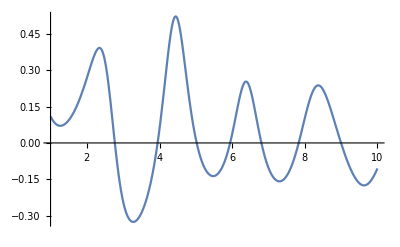

```mathematica
Plot[DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{k,1,10}]
```

### Manipulate

```mathematica
ClearAll[time,tabLarge];
time=AbsoluteTime[];
tabLarge=Table[
ClearAll[x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
{{k,by,rA,rB,rAθ,rBθ},DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},
{k,1,10,0.1},{by,0,5,1(*0.1*)},{rA,0.1,4,1(*0.2*)},{rB,0.1,4,1(*0.2*)},{rAθ,π/10,2π,π/2},{rBθ,π/10,2π,(*0.1*)π/2}]//Quiet;
AbsoluteTime[]-time
```

506.8201271

```mathematica
Flatten[tabLarge,1]
```

{1,2,{3}}

```mathematica
ClearAll[tabLarge1];
tabLarge1=Flatten[tabLarge,5];
```

```mathematica
ClearAll[tabLargeFun];
tabLargeFun=Interpolation[tabLarge1/.Indeterminate:>$Failed,InterpolationOrder->1];
```

```mathematica
Manipulate[{Show[Graphics[{Red,Disk[{rA/2 Cos[rAθ],by+rA/2 Sin[rAθ]},0.08]}],Graphics[{Blue,Disk[{-rA/2 Cos[rAθ],by-rA/2 Sin[rAθ]},0.08]}],Graphics[Line[{{rA/2 Cos[rAθ],by+rA/2 Sin[rAθ]},{-rA/2 Cos[rAθ],by-rA/2 Sin[rAθ]}}]],Graphics[{Red,Thick,Circle[{rB/2 Cos[rBθ],rB/2 Sin[rBθ]},0.08]}],Graphics[{Blue,Thick,Circle[{-rB/2 Cos[rBθ],-rB/2 Sin[rBθ]},0.08]}],Graphics[Line[{{rB/2 Cos[rBθ],rB/2 Sin[rBθ]},{-rB/2 Cos[rBθ],-rB/2 Sin[rBθ]}}]],Graphics[{Dashed,Line[{{0,0},{0,by}}]}],PlotRange->{{-3,3},{-3,8}},ImageSize->Medium,Frame->True],Plot[tabLargeFun[k,by,rA,rB,rAθ,rBθ],{k,1,10},PlotRange->{{1,10},{-0.5,0.5}},Frame->True,FrameLabel->{"kT","v_2"},ImageSize->Large]},{by,0,5,1(*0.1*)},{rA,0.1,4,1(*0.2*)},{rB,0.1,4,1(*0.2*)},{rAθ,π/10,3/2 π+π/10,π/2},{rBθ,π/10,3/2 π+π/10,(*0.1*)π/2}]//Quiet
```